## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
NotebookEvaluate[AbsoluteFileName["PlotFunctions.nb"]];
```

Import all the files required. Clade b alternate analysis commented out.

```mathematica
SetDirectory["../H5Output"];
dat1074=ImportStructuredHDF5["trialanalysis10-1074.h5"];
dat3BNC=ImportStructuredHDF5["trialanalysis3BNC.h5"];
datcombo=ImportStructuredHDF5["trialanalysiscombo.h5"];
datsnp=ImportStructuredHDF5["snpanalysis.h5"];
colorlist=ImportStructuredHDF5["colorlist.h5"];(**)
(*datsnpcladeb=ImportStructuredHDF5["snpanalysis_cladeb.h5"];*)
histogramdata=ImportStructuredHDF5["histogramdata.h5"];
trank = ImportStructuredHDF5["therapy_ranking.h5"];
mutH5 =ImportStructuredHDF5["trialsimulations_mutvsnomut.h5"];
traces = ImportStructuredHDF5["trialsimulations_traces.h5"];
SetDirectory[NotebookDirectory[]];
```

## Colors for antibody regions

```mathematica
colortab=<|"CD4 bs"->RGBColor[0.48, 0.39, 0.29],"Interface"->RGBColor[{0.6901960784313725, 0.47843137254901963, 0.6313725490196078}],"Loop D"->RGBColor[{0.9490196078431372, 0.5568627450980392, 0.16862745098039217}],"MPER"->RGBColor[{0.34901960784313724, 0.6313725490196078, 0.30980392156862746}],"V2"->RGBColor[{0.3058823529411765, 0.4745098039215686, 0.6549019607843137}],"V3"->RGBColor[{0.8823529411764706, 0.3411764705882353, 0.34901960784313724}],"V5 & beta23-24"->RGBColor[{0.4627450980392157, 0.7176470588235294, 0.6980392156862745}]|>
```

<|CD4 bs→RGBColor[0.48, 0.39, 0.29],Interface→RGBColor[{0.6901960784313725, 0.47843137254901963, 0.6313725490196078}],Loop D→RGBColor[{0.9490196078431372, 0.5568627450980392, 0.16862745098039217}],MPER→RGBColor[{0.34901960784313724, 0.6313725490196078, 0.30980392156862746}],V2→RGBColor[{0.3058823529411765, 0.4745098039215686, 0.6549019607843137}],V3→RGBColor[{0.8823529411764706, 0.3411764705882353, 0.34901960784313724}],V5 & beta23-24→RGBColor[{0.4627450980392157, 0.7176470588235294, 0.6980392156862745}]|>

```mathematica
escapeRegion[site_]:=
If[Length[#]<1,Nothing,Sequence[#]]&@Table[
If[And[Normal@colorlist["regions",key,"start"]≤site,
site≤Normal@colorlist["regions",key,"end"]],key,Nothing],{key,Keys[colorlist["regions"]]}]
locationsMap =Association[Table[ab->Commonest[Flatten@Table[escapeRegion[datsnp[ab,key,"loc"]]/.
"Loop D" -> "CD4 bs",{key,Keys[datsnp[ab]]}]][[1]],{ab,DeleteCases["101074"]@DeleteCases["VRC01_dms"]@Keys[datsnp]}]];
abcolormap=colortab/@locationsMap
```

<|10-1074→RGBColor[{0.8823529411764706, 0.3411764705882353, 0.34901960784313724}],10E8→RGBColor[{0.34901960784313724, 0.6313725490196078, 0.30980392156862746}],3BNC117→RGBColor[0.48, 0.39, 0.29],PG9→RGBColor[{0.3058823529411765, 0.4745098039215686, 0.6549019607843137}],PGT121→RGBColor[{0.8823529411764706, 0.3411764705882353, 0.34901960784313724}],PGT145→RGBColor[{0.3058823529411765, 0.4745098039215686, 0.6549019607843137}],PGT151→RGBColor[{0.6901960784313725, 0.47843137254901963, 0.6313725490196078}],VRC01→RGBColor[0.48, 0.39, 0.29],VRC34→RGBColor[{0.6901960784313725, 0.47843137254901963, 0.6313725490196078}]|>

```mathematica
getColor[site_]:=Module[{col},
col = RGBColor[Normal@colorlist["regions",#,"color"]]&/@escapeRegion[site];
If[col == Nothing,Return[LightGray]];
Return[col];]
```

```mathematica
ImExport["gp160",Show[Graphics[{Lighter[LightGray,.8],Rectangle[{0,-31},{30,-699}]}],Graphics[Flatten@Table[
{colortab[key],Rectangle[
{0,-Normal@colorlist["regions",key,"start"]},{30,-Normal@colorlist["regions",key,"end"]}
]},{key,
(*Select[Keys[colorlist["regions"]],Or[ElementQ[#,locationsMap],#=="CD4 bs"]&]*)
Keys[colorlist["regions"]]
}]],Frame->True,LabelStyle->fontopts,FrameStyle->AbsoluteThickness[1],FrameLabel->{{"Site (HXB2 AA locus)",None},{None,None}},FrameTicks->{Reverse@{None,Transpose[{-Range[100,600,100],ToString/@Range[100,600,100]}]},{None,None}}],{31/699,1}]
```

Figures/gp160.pdf

```mathematica
table[pairs_]:=TableForm[pairs,TableAlignments->Left,TableSpacing->{2,1}];
ImExport["gp160_legends",Plot[{},{x,0,1},Frame->False,PlotLegends->Placed[SwatchLegend[Sequence@@Transpose[Table[
{colortab[key],StringReplace[key,{"beta"->"β"," & "->"/"}]},
(*If[Or[ElementQ[key,locationsMap],key=="CD4 bs"],
{RGBColor[Normal@colorlist["regions",key,"color"]],key},Nothing],*){key,SortBy[Keys[colorlist["regions"]],Normal@colorlist["regions",#,"start"]&]}]],LegendLayout->table],{.5,.5}],AspectRatio->1],{1,1}]
```

Figures/gp160_legends.pdf

### Table of decay rates

```mathematica
TableForm[Table[{dat["viraemic","decay"]},{dat,{dat1074,dat3BNC,datcombo}}]]
```

0.364227
0.228763
0.333933

## Bayesian Posterior

```mathematica
x=Apply[Labeled,Table[
SortBy[Table[
If[Mean[#]<0,Nothing,{Style[Log10@#,
getColor[datsnp[ab,site,"loc"]]
],Rotate[StringReplace[site,{"site"->""}],π/2]}]&
[Normal[datsnp[ab,site,"bayes_avg1.0"]]],{site,Keys[datsnp[ab]]}]
,Mean[#[[1,1]]]&],{ab,DeleteCases[DeleteCases["VRC01_dms"]@Keys[datsnp],"101074"]}],{2}];
```

```mathematica
(*x=Apply[Labeled,Table[
SortBy[Table[
If[Mean[#]<0,Nothing,{Style[Log10@#,
getColor[datsnp[ab,site,"loc"]]
],Rotate[StringReplace[site,{"site"->""}],π/2]}]&
[Normal[datsnp[ab,site,"bayes_avg0.0"]]],{site,Keys[datsnp[ab]]}]
,Mean[#[[1,1]]]&],{ab,DeleteCases[DeleteCases["VRC01_dms"]@Keys[datsnp],"101074"]}],{2}];*)
```

```mathematica
(*x=Apply[Labeled,Table[
SortBy[Table[
If[Mean[#]<0,Nothing,{Style[Log10@#,
getColor[datsnp[ab,site,"loc"]]
],Rotate[StringReplace[site,{"site"->""}],π/2]}]&
[Normal[datsnpcladeb[ab,site,"bayes_avg1.0"]]],{site,Keys[datsnp[ab]]}]
,Mean[#[[1,1]]]&],{ab,DeleteCases[DeleteCases["VRC01_dms"]@Keys[datsnp],"101074"]}],{2}];*)
```

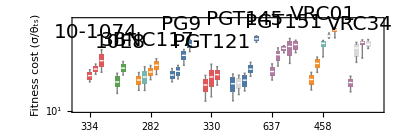

```mathematica
plt=BoxWhiskerChart[
x,BarSpacing->{.5,2},
Method->{"BoxRange"->(Quantile[#,{.1,1/4,1/2,3/4,.9}]&)},PlotRange->{{-1,50},{1,4.2}},FrameLabel->{"Site (HXB2 AA locus)","Fitness cost (σ/θ_ts)"},
AspectRatio->1/3,
FrameTicksStyle->{Directive[FontSize->18],Directive[FontSize->16]},
LabelStyle->{FontFamily->"Arial",FontSize->20,FontColor->GrayLevel[0]},
FrameStyle->AbsoluteThickness[1],FrameTicks->{{LogTicks[10,1,100],LogTicks[10,1,4,ShowTickLabels->False]},{Automatic,None}},ChartLabels->{Placed[Text[Style[#,abcolormap[#],FontWeight->Bold,FontSize->18]]&/@DeleteCases[DeleteCases["VRC01_dms"]@Keys[datsnp],"101074"],Above],None}
]
```

```mathematica
ImExport["FitnessUncertainties",plt,{3,1}]
```

Figures/FitnessUncertainties.pdf

## Rebound probability ranking

Include the clinical trials that don’t show up on the ranking

```mathematica
MakeTrialLine[name_][x_,y_]:=Module[{d,colorlist},
d = .07;
colorlist=Association[aminoColorScheme]/@{"P","P","P"};
{Black,AbsoluteThickness[1],Line[{{x,Min[y]},{x,Max[y]}}],Line[{{x-d,Min[y]},{x+d,Min[y]}}],
Line[{{x-d,Max[y]},{x+d,Max[y]}}],AbsolutePointSize[4],Point[{x,y[[2]]}],Black,MapIndexed[
Function[{xx,yy},Text[Style[xx,abcolormap[xx],FontWeight->Bold,FontSize->16,FontFamily->"Arial"],{x,Min[y]+.08},{0,2Sequence@@yy}]],
name]
}]
```

```mathematica
XRankKey[x_,rank_,key_]:=Module[{names,y},
names=trank[rank,key,"therapy"];
y=Quantile[Log10@Normal@trank[rank,key,"rebounds"],{.25,.5,.75}];MakeTrialLine[names][x,y]]
```

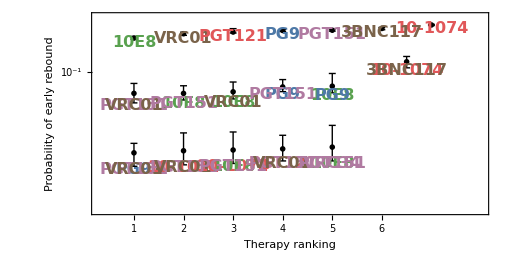

```mathematica
plt=Show[Plot[{},{x,.3,8},PlotRange->{-3.5,0},FrameTicks->{{LogTicks[-10,2,TickLabelStep->1],LogTicks[-10,2,ShowTickLabels->False]},{LinTicks[1,6,1,1],LinTicks[1,6,1,1,ShowTickLabels->False]}},FrameLabel->{"Therapy ranking","Probability of early rebound"},AspectRatio->5/10],
Module[{sortedKeys},
Table[
sortedKeys=
SortBy[Keys[trank[rank]],Function[key,Median[Log@Normal@trank[rank,key,"rebounds"]]]];
Graphics@Table[
XRankKey[ii,rank,sortedKeys[[ii]]]
,{ii,1,5}],
{rank,Keys[trank]}]],
Graphics@XRankKey[6.5,"2_antibodies","10-10743BNC117"],
Graphics@XRankKey[7,"1_antibodies","10-1074"],
Graphics@XRankKey[6,"1_antibodies","3BNC117"]
]
```

```mathematica
ImExport["TherapyRanking",plt,{2,1}]
```

Figures/TherapyRanking.pdf

## Make the histograms

```mathematica
ThetaVec[dat_]:=Flatten@Table[If[day["day"]<1,day["theta"],Nothing],{patient,dat["genetic"]},{day,patient}]
getxs[dat_]:=Values[#["x"]&/@dat["viraemic","patients"]]
getpars[dat_]:=Values[{#["rsel"][[1]],Normal[#["mut"]]}&/@dat]
SimPars[parlist_,thetalist_]:=Flatten@Table[Table[1-Times@@Table[RandomWrightSample@@(s*p),{s,parlist}],
{p,thetalist}],{4000}];
SimCombo[parlists_,thetalist_]:=Flatten@Table[
Table[
Times@@Table[1-Times@@Table[RandomWrightSample@@(s*p),{s,parlist}],{parlist,parlists}],
{p,thetalist}],{4000}];
multisim[dattrial_,datsnps_][diversitymultiplier_,selectionmultiplier_]:=Module[{xs,thetas,pars},
thetas=ThetaVec[dattrial];
pars=Table[getpars[datsnp],{datsnp,datsnps}];
SimCombo[Map[{selectionmultiplier*#[[1]],#[[2]]}&,pars,{2}],diversitymultiplier*thetas]];
Thetasim[theta_,datsnps_]:=Module[{xs,pars},
pars=Table[getpars[datsnp],{datsnp,datsnps}];
SimCombo[Map[{#[[1]],#[[2]]}&,pars,{2}],{theta}]];
sim[dattrial_,datsnps_][diversitymultiplier_,selectionmultiplier_]:=Module[{xs,thetas,pars},
thetas=ThetaVec[dattrial];
pars=getpars[datsnps];
SimPars[{selectionmultiplier*#[[1]],#[[2]]}&/@pars,diversitymultiplier*thetas]];
trimlog[xx_]:=-3Log[If[#>.90,#+1,Max[#,10^(-30.)]]]&/@xx
trimzero[xx_]:=If[#<1,#-1,#]&/@xx
```

```mathematica
histogramdata
```

<|10-1074→NumericArray[…],combo→NumericArray[…],10-1074ref→NumericArray[…],3BNCref→NumericArray[…],3BNC→NumericArray[…],comboref→NumericArray[…]|>

```mathematica
removed=Drop[Sort[getxs[dat3BNC]],-3]; (*Drop the three non responders associated with low-doses*)
```

```mathematica
(*removed 3 nonresponders associated with low dose cohort*)
```

Generate the histograms with and without (“ref”) reservior factor

```mathematica
Table[ImExport["histopred1074"<>key,HistoErrors[trimlog@getxs[dat1074],trimzero[Flatten@Normal@histogramdata["10-1074"<>key]],{0,56,7}],{1,1}];
ImExport["histopred3BNC"<>key,HistoErrors[trimlog@removed,trimzero[Flatten@Normal@histogramdata["3BNC"<>key]],{0,56,7}],{1,1}];
ImExport["histopredcombo"<>key,HistoErrors[trimlog@getxs[datcombo],trimzero[Flatten@Normal@histogramdata["combo"<>key]],{0,56,7}],{1,1}];,{key,{"","ref"}}]
```

## Effect Of Mutations

```mathematica
plt=Show[Plot[{},{x,0,56},PlotRange->{{0,56},{-5.3,0.2}},AspectRatio->4/5,
FrameTicks->{{LogTicks[-5,0],LogTicks[-5,0,ShowTickLabels->False]},{LinTicks[0,56,14,2],LinTicks[0,56,14,2,ShowTickLabels->False]}},FrameLabel->{"Time since treatment (days)","Mutant pop-size (N_k^-1)"}],Module[{array =Normal[ traces["10-1074"]],xx,yy},
xx=array[[1,;;,1]];
Graphics[Join[{Opacity[.1],AbsoluteThickness[.5]},Table[
yy =Normal[traces["10-1074"]][[ii,;;,1]];
If[Total[yy]>0,
Line[Transpose@{xx,Log10[yy+10^-10]}],Nothing],
{ii,2,1601}],{}
(*{Opacity[1],Darker[Red],AbsoluteThickness[1], Line[{{0,-4},{25,-4}}], 
Darker[Orange],Line[{{0,-5},{20,-5}}]}*)
]]]]
```

-Graphics-

```mathematica
ImExport["mutanttraces",plt,{5/4,1}]
```

Figures/mutanttraces.pdf

```mathematica
ImExport["extinctintion_threshold",Show[Plot[{},{x,0,56},PlotRange->{{0,56},{-5.3,0.2}},
FrameTicks->{{LogTicks[-5,0],LogTicks[-5,0,ShowTickLabels->False]},{LinTicks[0,56,7,7],LinTicks[0,56,7,7,ShowTickLabels->False]}},FrameLabel->{"Time since treatment (days)","Mutant pop-size (K^-1)"}],Module[{array =Normal[ traces["10-1074"]],xx,yy},
xx=array[[1,;;,1]];
Graphics[Join[{Opacity[.1],AbsoluteThickness[.5]},Table[
yy =Normal[traces["10-1074"]][[ii,;;,1]];
If[Total[yy]>0,
Line[Transpose@{xx,Log10[yy+10^-10]}],Nothing],
{ii,2,1600}],
{Opacity[1],Darker[Red],AbsoluteThickness[1], Line[{{0,-4},{25,-4}}], 
Darker[Orange],Line[{{0,-5},{20,-5}}]}
]]]],{8/5,1}]
```

Figures/extinctintion_threshold.pdf

```mathematica
mutH5 =ImportStructuredHDF5["trialsimulations_mutvsnomut.h5"];
```

```mathematica
Table[{#[[1]],#[[1]]-#[[2]]}&@Normal[mutH5[key]],{key,Keys[mutH5]}]
```

{{0.274571,0.00342857},{0.530294,0.0138187},{0.500456,0.0325833}}

```mathematica
ImExport["standing_variation_vs_mutation_bar2",BarChart[Table[{#[[2]],#[[1]]-#[[2]],1-#[[1]]}&@Normal[mutH5[key]],{key,{"10-1074","3BNC117","combo"}}],PlotRange->{{.4,3.6},{0,1}},BarSpacing->{1,.5},ChartLayout->"Stacked",FrameLabel->{None,"Frequency"},ChartStyle->(Directive[EdgeForm[None],#]&/@{RGBColor[1., 0.93, 0.48],RGBColor[0.62, 0., 0.28],RGBColor[0.56, 0.88, 1.]}),AspectRatio->1/0.4,ChartLabels->{Rotate[Text[#],π/2]&/@{"10-1074","3BNC117","Combo"},None},ChartLegends->Placed[{"Standing var. esc","Mut. esc.","Late rebound"},{Right,Right}]],{.4,1}]
```

Figures/standing_variation_vs_mutation_bar2.pdf

## Harmonic-mean vs mut target size

```mathematica
LogHarmonicMeanDist[ab_]:=Module[{sites},
sites =DeleteCases[ Keys[datsnp[ab]],"site85"];
Log10@Quantile[Table[HarmonicMean[Table[RandomChoice[Normal@datsnp[ab,site,"bayes_avg1.0"]],{site,sites}]],1000],{.25,.5,.75}]
]
```

```mathematica
LogHarmonicMeanLine[ab_]:=Module[{x,d},
x=Plus@@Table[datsnp[ab,site,"mut"][[1]],{site,DeleteCases[Keys[datsnp[ab]],"site85"]}];
If[ab=="VRC01",x+=-.1]; (*Shift VRC01 for visualization*)
d=.04;
{abcolormap[ab],AbsoluteThickness[2],Line[{{x,Min[#]},{x,Max[#]}}],Line[{{x-d,Min[#]},{x+d,Min[#]}}],
Line[{{x-d,Max[#]},{x+d,Max[#]}}],AbsolutePointSize[4],Point[{x,#[[2]]}],Black,Style[Text[" "<>ab<>" ",{x,#[[2]]},
Switch[ab, (*Label Placement*)
"10E8",{.94,0},
"VRC01",{.94,0},
"VRC34",{-.5,3.6},
"3BNC117",{0,3.2},
"PGT121",{.92,1.0},
"10-1074",{0,2.5},
"PGT151",{-1,0},
_,{-1.0,0}
]],FontSize->16,abcolormap[ab],FontWeight->Bold]}&@LogHarmonicMeanDist[ab]]
```

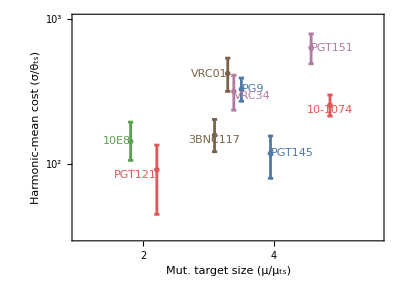

```mathematica
plt=Show[Plot[{},{x,1,5.6},PlotRange->{1.5,3},FrameTicks->{{LogTicks[1,7,TickLabelStep->1],LogTicks[1,7,ShowTickLabels->False]},{LinTicks[0,8],LinTicks[1,7,ShowTickLabels->False]}},AspectRatio->1/1.4,FrameLabel->{"Mut. target size (µ/µ_ts)","Harmonic-mean cost (σ/θ_ts)"}],Graphics[Join@@Table[LogHarmonicMeanLine[ab],{ab,Complement[Keys[datsnp],{"101074","VRC01_dms"}]}]]]
```

```mathematica
ImExport["harmonic_selection_vs_muational_target",plt,{1.4,1}]
```

Figures/harmonic_selection_vs_muational_target.pdf